```mathematica
SetDirectory[NotebookDirectory[]]

"/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks"

(*LOAD FUNCTIONS*)

<<MyFunctions`

(*INIITIALIZE PARAMETERS*)
alpha=0.5;
beta=1.0;
delta=0.5;
katta=5;
qAvg=1.0;
eta=0.25;
etaBar=0.5;
chi=0.1;
uBar=1.0;
cp=20.0;
cs=10.0;

(*Number of firms*)
n=10.0;
(*A dummy vector used to identify each firm by a certain number:1-first firm,2-second firm,.....n-nth firm*)
Id=Table[i,{i,1,n}];

(*Number of consumers*)
m=100.0;
```

/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks

/home/dominic/Dokumente/Science/Econ/Computational Economics/Praktische Übung/Projekt-Industriedynamik/Notebooks

------------------------------------------------------------------------------------------------------------------------------

Exercise 1 b)

------------------------------------------------------------------------------------------------------------------------------

------------------------------------------------------------------------------------------------------------------------------

Results batch runs:

------------------------------------------------------------------------------------------------------------------------------

Number of firms that survive: {5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}

The firms which survive: 1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

------------------------------------------------------------------------------------------------------------------------------

Results of last batch run:

------------------------------------------------------------------------------------------------------------------------------

Prices: 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
39.0313 | 39.0313 | 39.0313 | 39.0313 | 39.0313 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
41.3906 | 41.3906 | 41.3906 | 41.3906 | 41.3906 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
42.5703 | 42.5703 | 42.5703 | 42.5703 | 42.5703 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.1602 | 43.1602 | 43.1602 | 43.1602 | 43.1602 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.4551 | 43.4551 | 43.4551 | 43.4551 | 43.4551 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.6025 | 43.6025 | 43.6025 | 43.6025 | 43.6025 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.6763 | 43.6763 | 43.6763 | 43.6763 | 43.6763 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.7131 | 43.7131 | 43.7131 | 43.7131 | 43.7131 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5
43.7316 | 43.7316 | 43.7316 | 43.7316 | 43.7316 | 37.5 | 37.5 | 37.5 | 37.5 | 37.5

Null^2

Quality: 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
8. | 8. | 8. | 8. | 8. | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
13.2066 | 13.2066 | 13.2066 | 13.2066 | 13.2066 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
16.7797 | 16.7797 | 16.7797 | 16.7797 | 16.7797 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
19.6815 | 19.6815 | 19.6815 | 19.6815 | 19.6815 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
22.1896 | 22.1896 | 22.1896 | 22.1896 | 22.1896 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
24.4307 | 24.4307 | 24.4307 | 24.4307 | 24.4307 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
26.4755 | 26.4755 | 26.4755 | 26.4755 | 26.4755 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
28.3679 | 28.3679 | 28.3679 | 28.3679 | 28.3679 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949
30.1376 | 30.1376 | 30.1376 | 30.1376 | 30.1376 | 4.87298 | 3.82843 | 4.60555 | 4. | 3.44949

Market Share: 49/100
1
1
1
1
1
1
1
1
1

Profits: 52.5 | 60. | 90. | 75. | 90. | 112.5 | 60. | 97.5 | 67.5 | 45.
195.156 | 163.931 | 187.35 | 109.287 | 124.9 | 0. | 0. | 0. | 0. | 0.
190.397 | 115.894 | 206.953 | 124.172 | 190.397 | 0. | 0. | 0. | 0. | 0.
187.309 | 221.366 | 110.683 | 161.767 | 170.281 | 0. | 0. | 0. | 0. | 0.
103.584 | 172.641 | 172.641 | 198.537 | 215.801 | 0. | 0. | 0. | 0. | 0.
173.82 | 156.438 | 156.438 | 165.129 | 217.275 | 0. | 0. | 0. | 0. | 0.
122.087 | 156.969 | 244.174 | 174.41 | 174.41 | 0. | 0. | 0. | 0. | 0.
131.029 | 165.97 | 165.97 | 218.381 | 192.176 | 0. | 0. | 0. | 0. | 0.
113.654 | 157.367 | 209.823 | 183.595 | 209.823 | 0. | 0. | 0. | 0. | 0.
122.448 | 174.926 | 166.18 | 192.419 | 218.658 | 0. | 0. | 0. | 0. | 0.

Period Qunatities: 7 | 8 | 12 | 10 | 12 | 15 | 8 | 13 | 9 | 6
25 | 21 | 24 | 14 | 16 | 0 | 0 | 0 | 0 | 0
23 | 14 | 25 | 15 | 23 | 0 | 0 | 0 | 0 | 0
22 | 26 | 13 | 19 | 20 | 0 | 0 | 0 | 0 | 0
12 | 20 | 20 | 23 | 25 | 0 | 0 | 0 | 0 | 0
20 | 18 | 18 | 19 | 25 | 0 | 0 | 0 | 0 | 0
14 | 18 | 28 | 20 | 20 | 0 | 0 | 0 | 0 | 0
15 | 19 | 19 | 25 | 22 | 0 | 0 | 0 | 0 | 0
13 | 18 | 24 | 21 | 24 | 0 | 0 | 0 | 0 | 0
14 | 20 | 19 | 22 | 25 | 0 | 0 | 0 | 0 | 0

Markup Specialist:, 0.
0.1225
0.31125
0.405625
0.452813
0.476406
0.488203
0.494102
0.497051
0.498525

Quant Agg. Spec0.
49.
149.
249.
349.
449.
549.
649.
749.
849.

Market Share: 49/100
1
1
1
1
1
1
1
1
1

------------------------------------------------------------------------------------------------------------------------------

Plots of last batch run:

------------------------------------------------------------------------------------------------------------------------------

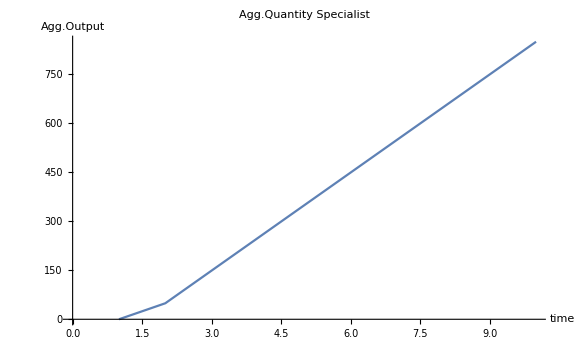

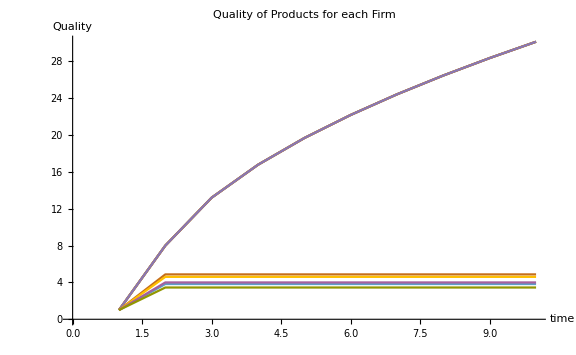

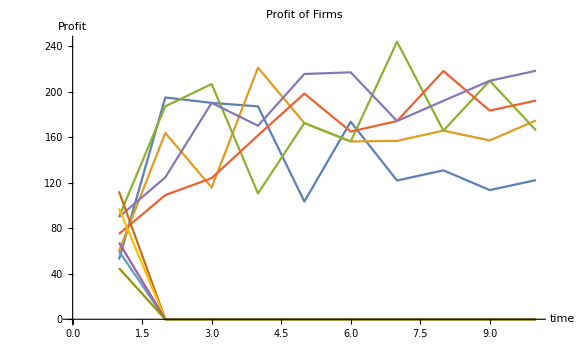

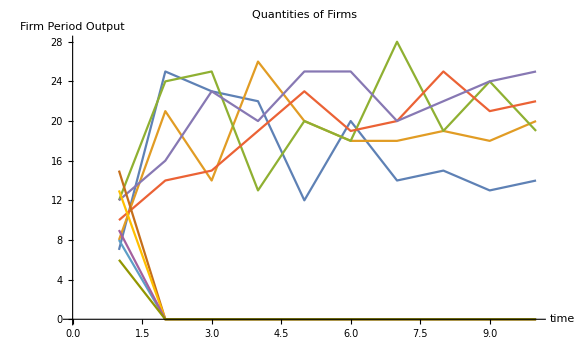

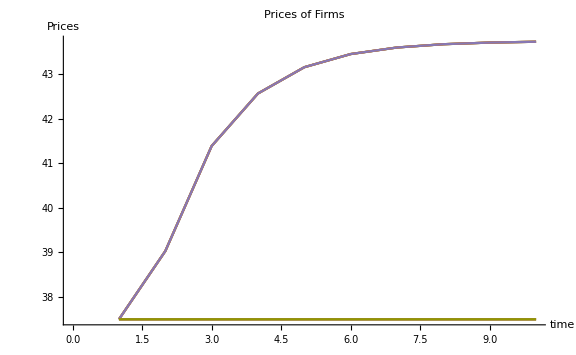

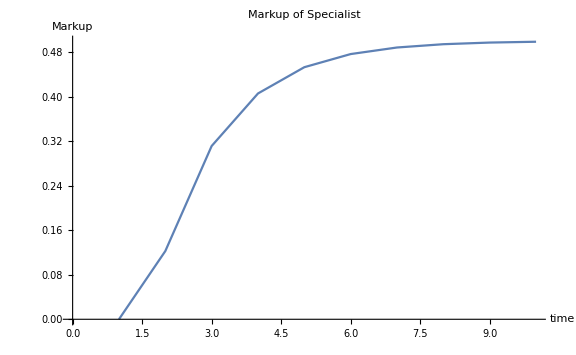

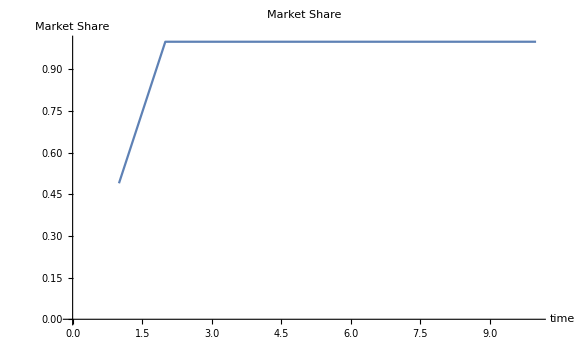

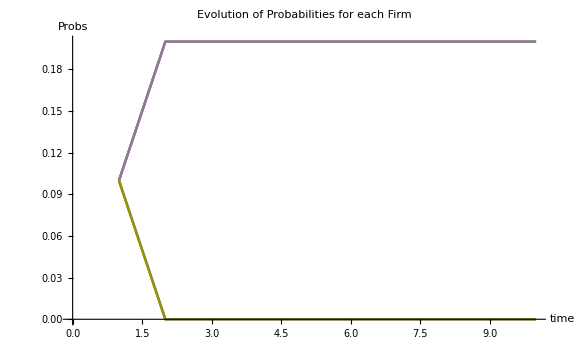

```mathematica
T=10;
R=20;
(*firms making positive profits at T for each batch run*)

survivor=Table[0.0,{r,1,R}];
(*how many firms make positive profits at T?*)

numFirmsSurvive=Table[0.0,{r,1,R}];


Do[
priceListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
priceSpec=Table[0.0,{i,1,T}];
quantPeriodFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
quantPeriodSpec=Table[0.0,{i,1,T}];
quantAggSpec=Table[0.0,{i,1,T}];
quantAggFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];
msSpec=Table[0.0,{i,1,T}];
markupSpec=Table[0.0,{i,1,T}];
qualityList=Table[Table[0.0,{i,1,n}],{i,1,T}];
probList=Table[Table[0.0,{i,1,n}],{i,1,T}];
profitListFirm=Table[Table[0.0,{i,1,n}],{i,1,T}];

(*PERIODS*)
Do[
(*compute aggregated quantities for each firm*)
If[t==1,quantAggFirm[[t]]=Table[0.0,{i,1,n}],
quantAggFirm[[t]]=Table[quantAggFirm[[t-1,i]]+quantPeriodFirm[[t-1,i]],{i,1,n}]];
(*compute aggregated quantities of specialist*)
If[t==1,quantAggSpec[[t]]=0.0,
quantAggSpec[[t]]=quantAggSpec[[t-1]]+quantPeriodSpec[[t-1]]];
(*compute markup*)
If[t==1,markupSpec[[t]]=0.0,
markupSpec[[t]]=etaSpec[delta,markupSpec[[t-1]],msSpec[[t-1]],etaBar]];
(*compute price of specialist*)
priceSpec[[t]]=pSpec[cs,markupSpec[[t]]];
(*compute prices*)
Do[priceListFirm[[t,i]]=pFirmSpec[cSpec[cp,cs,markupSpec[[t]]],eta],{i,1,5}];
Do[priceListFirm[[t,i]]=pFirmSelf[cSelf[cp,cs],eta],{i,6,n}];
(*compute qualities*)
Do[qualityList[[t,i]]=qualitySpec[uBar,alpha,beta,quantAggSpec[[t]]],{i,1,5}];
Do[qualityList[[t,i]]=qualityFirm[uBar,alpha,beta,quantAggFirm[[t,i]]],{i,6,n}];
(*compute probabilities*)
probList[[t]]=Table[probability[i,priceListFirm[[t]],qualityList[[t]]],{i,1,n}];
(*compute demand*)
choiceListAll=RandomChoice[probList[[t]]->Id,m];
(*compute period output*)
quantPeriodFirm[[t]]=Table[Count[choiceListAll,i],{i,1,n}];
quantPeriodSpec[[t]]=Sum[quantPeriodFirm[[t,i]],{i,1,5}];
(*compute market share*)
msSpec[[t]]=ms[t,n,quantPeriodSpec[[t]],quantPeriodFirm];
(*compute profits*)
Do[profitListFirm[[t,i]]=profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSpec[cp,cs,markupSpec[[t]]]],{i,1,5}];
Do[profitListFirm[[t,i]]=profit[quantPeriodFirm[[t,i]],priceListFirm[[t,i]],cSelf[cp,cs]],{i,6,n}];
(*compute statistic*)
If[t==T,numFirmsSurvive[[r]]=Count[profitListFirm[[t]],u_/;u>0];
survivor[[r]]=Position[profitListFirm[[t]],u_/;u>0]],

{t,1,T}],
{r,1,R}]

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Exercise 1 b)"]
Print["------------------------------------------------------------------------------------------------------------------------------"]

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Results batch runs:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Number of firms that survive: ",numFirmsSurvive]
Print["The firms which survive: ",TableForm[Table[Table[survivor[[r,i,1]],{i,1,Length[survivor[[r]]]}],{r,1,R}]]]

Print["------------------------------------------------------------------------------------------------------------------------------"] 
Print["Results of last batch run:"] 
Print["------------------------------------------------------------------------------------------------------------------------------"]Print["Prices: ",TableForm[priceListFirm]]
 Print["Quality: ",TableForm[qualityList]] 
Print["Market Share: ",TableForm[msSpec]] 
Print["Profits: ",TableForm[profitListFirm]] 
Print["Period Qunatities: ",TableForm[quantPeriodFirm]] 
Print["Markup Specialist:, ",TableForm[markupSpec]]
 Print["Quant Agg. Spec",TableForm[quantAggSpec]]
Print["Market Share: ", TableForm[msSpec]]

Print["------------------------------------------------------------------------------------------------------------------------------"]
Print["Plots of last batch run:"]
Print["------------------------------------------------------------------------------------------------------------------------------"]
ListPlot[quantAggSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Agg.Quantity Specialist],AxesLabel->{HoldForm[time],HoldForm[Agg.Output]}]
ListPlot[Table[Table[qualityList[[t,j]],{t,1,T}],{j,1,n}],Joined->True,ImageSize->Large,PlotLabel->HoldForm[Quality of Products for each Firm],AxesLabel->{HoldForm[time],HoldForm[Quality]}]
(*plot profit of each firm*)
ListPlot[Table[Table[profitListFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True,PlotRange->All,ImageSize->Large,PlotLabel->HoldForm[Profit of Firms],AxesLabel->{HoldForm[time],HoldForm[Profit]}]
(*plot determinants of profit*)
ListPlot[Table[Table[quantPeriodFirm[[t,j]],{t,1,T}],{j,1,n}],Joined->True,ImageSize->Large,PlotLabel->HoldForm[Quantities of Firms],AxesLabel->{HoldForm[time],HoldForm[Firm Period Output]}]
ListPlot[Table[Table[priceListFirm[[t,j]],{t,1,T}],{j,1,n}],PlotRange->All,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Prices of Firms],AxesLabel->{HoldForm[time],HoldForm[Prices]}]
ListPlot[markupSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Markup of Specialist],AxesLabel->{HoldForm[time],HoldForm[Markup]}]
ListPlot[msSpec,Joined->True,ImageSize->Large,PlotLabel->HoldForm[Market Share],AxesLabel->{HoldForm[time],HoldForm[Market Share]}]
ListPlot[Table[Table[probList[[t,j]],{t,1,10}],{j,1,n}],Joined->True,PlotRange->All,ImageSize->Large,PlotLabel->HoldForm[Evolution of Probabilities for each Firm],AxesLabel->{HoldForm[time],HoldForm[Probs]}]
```